```mathematica
(* We solve two 2-beam equations, one for the Lyman photons, with absorption κ and scattering σL and one for the H-alpha photons.
The two beams for the Lyman photons are  ILp (in the plus direction) and ILm.
For the Hα photons, they are IHp and IHm *)
```

```mathematica
(* These are the two equations for the lyman photons *)
```

```mathematica
sol1=FullSimplify[DSolve[{
ILp'[x]==  -(κT +σL)ILp[x]+σL/2(ILp[x]+ILm[x]),
-ILm'[x]==-(κT +σL)ILm[x]+σL/2(ILp[x]+ILm[x])
},{ILp[x],ILm[x]},x]]⟦1⟧
```

{ILm[x]→C[1] Cosh[x √(κT (κT+σL))]+(((2 κT+σL) C[1]-σL C[2]) Sinh[x √(κT (κT+σL))])/(2 √(κT (κT+σL))),ILp[x]→C[2] Cosh[x √(κT (κT+σL))]+((σL C[1]-(2 κT+σL) C[2]) Sinh[x √(κT (κT+σL))])/(2 √(κT (κT+σL)))}

```mathematica
(* This is the solution for the Ly-plus *)
```

```mathematica
ILpsol=ILp[x] /. sol1
```

C[2] Cosh[x √(κT (κT+σL))]+((σL C[1]-(2 κT+σL) C[2]) Sinh[x √(κT (κT+σL))])/(2 √(κT (κT+σL)))

```mathematica
(* This is the solution for the Ly-minus *)
```

```mathematica
ILmsol=ILm[x] /. sol1
```

C[1] Cosh[x √(κT (κT+σL))]+(((2 κT+σL) C[1]-σL C[2]) Sinh[x √(κT (κT+σL))])/(2 √(κT (κT+σL)))

```mathematica
(* Now we impose the boundary conditions. An Influx at x=0 and no influx at x=d *)
```

```mathematica
(* Modified: An *net* Influx at x=0 and no influx at x=d *)
```

```mathematica
Csol=Solve[{(ILpsol-ILmsol /. x->0)==Iin,(ILmsol /. x->d)==0},{C[1],C[2]}]⟦1⟧
```

{C[1]→(Iin σL √(κT (κT+σL)) Sinh[d √(κT (κT+σL))])/(2 κT (κT+σL) (Cosh[d √(κT (κT+σL))]+(√(κT (κT+σL)) Sinh[d √(κT (κT+σL))])/(κT+σL))),C[2]→(Iin (2 κT^2 Cosh[d √(κT (κT+σL))]+2 κT σL Cosh[d √(κT (κT+σL))]+2 κT √(κT (κT+σL)) Sinh[d √(κT (κT+σL))]+σL √(κT (κT+σL)) Sinh[d √(κT (κT+σL))]))/(2 κT (κT Cosh[d √(κT (κT+σL))]+σL Cosh[d √(κT (κT+σL))]+√(κT (κT+σL)) Sinh[d √(κT (κT+σL))]))}

```mathematica
(* ILpSol is with the boundary conditions. ILpsol is the general without boundary conditions *)
```

```mathematica
ILpSol=FullSimplify[Expand[ILpsol /. Csol]]
```

(Iin (2 κT (κT+σL) Cosh[(d-x) √(κT (κT+σL))]+√(κT (κT+σL)) (2 κT+σL) Sinh[(d-x) √(κT (κT+σL))]))/(2 κT ((κT+σL) Cosh[d √(κT (κT+σL))]+√(κT (κT+σL)) Sinh[d √(κT (κT+σL))]))

```mathematica
ILmSol=FullSimplify[Expand[ILmsol /. Csol]]
```

(Iin σL √(κT (κT+σL)) Sinh[(d-x) √(κT (κT+σL))])/(2 κT ((κT+σL) Cosh[d √(κT (κT+σL))]+√(κT (κT+σL)) Sinh[d √(κT (κT+σL))]))

```mathematica
(* Lets plot the solution, for example for absorption that is 1/6 of the scattering, and optical depth of 10 scattering distances *)
```

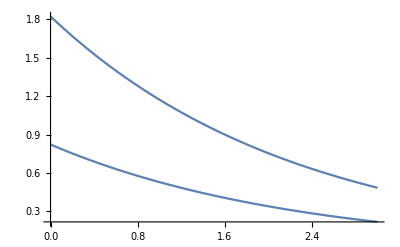

```mathematica
Plot[{ILpSol,ILmSol} /. σL->1 /. κT->1/6/. d->10/. Iin->1,{x,0,3},PlotRange->All]
```

```mathematica
(* This is the energy density of the Lyman photons, needed as a source for the Hα photons *)
```

```mathematica
ELSol=FullSimplify[ILpSol+ILmSol]
```

(Iin (κT+σL) (κT Cosh[(d-x) √(κT (κT+σL))]+√(κT (κT+σL)) Sinh[(d-x) √(κT (κT+σL))]))/(κT (κT+σL) Cosh[d √(κT (κT+σL))]+κT √(κT (κT+σL)) Sinh[d √(κT (κT+σL))])

```mathematica
(* And the actual two beam equations *)
```

```mathematica
sol2=FullSimplify[DSolve[{
IHp'[x]==  κR ELSol/2 -(σH+κH) IHp[x]+ σH/2(IHp[x]+IHm[x]),
-IHm'[x]==κR ELSol/2 - (σH+κH) IHm[x]+σH/2(IHp[x]+IHm[x])
},{IHp[x],IHm[x]},x]]⟦1⟧
```

{IHm[x]→C[1] Cosh[x √(κH (κH+σH))]+(((2 κH+σH) C[1]-σH C[2]) Sinh[x √(κH (κH+σH))])/(2 √(κH (κH+σH)))-(Iin κR (κT+σL) (κT (κH-κT+σH-σL) Cosh[(d-x) √(κT (κT+σL))]+(κH-κT+σH) √(κT (κT+σL)) Sinh[(d-x) √(κT (κT+σL))]))/(2 κT (-κH (κH+σH)+κT (κT+σL)) ((κT+σL) Cosh[d √(κT (κT+σL))]+√(κT (κT+σL)) Sinh[d √(κT (κT+σL))])),IHp[x]→1/4 (4 C[2] Cosh[x √(κH (κH+σH))]+(2 (σH C[1]-(2 κH+σH) C[2]) Sinh[x √(κH (κH+σH))])/(√(κH (κH+σH)))-(2 Iin κR (κT+σL) (κH+κT+σH+σL) Cosh[(d-x) √(κT (κT+σL))])/((-κH (κH+σH)+κT (κT+σL)) ((κT+σL) Cosh[d √(κT (κT+σL))]+√(κT (κT+σL)) Sinh[d √(κT (κT+σL))]))+(2 Iin κR (κH+κT+σH) (κT+σL) Sinh[(d-x) √(κT (κT+σL))])/((κH (κH+σH)-κT (κT+σL)) (√(κT (κT+σL)) Cosh[d √(κT (κT+σL))]+κT Sinh[d √(κT (κT+σL))])))}

```mathematica
(* General plus direction and minus direction solutions *)
```

```mathematica
IHpsol=FullSimplify[IHp[x] /. sol2 ]
```

1/4 (4 C[2] Cosh[x √(κH (κH+σH))]+(2 (σH C[1]-(2 κH+σH) C[2]) Sinh[x √(κH (κH+σH))])/(√(κH (κH+σH)))-(2 Iin κR (κT+σL) (κH+κT+σH+σL) Cosh[(d-x) √(κT (κT+σL))])/((-κH (κH+σH)+κT (κT+σL)) ((κT+σL) Cosh[d √(κT (κT+σL))]+√(κT (κT+σL)) Sinh[d √(κT (κT+σL))]))+(2 Iin κR (κH+κT+σH) (κT+σL) Sinh[(d-x) √(κT (κT+σL))])/((κH (κH+σH)-κT (κT+σL)) (√(κT (κT+σL)) Cosh[d √(κT (κT+σL))]+κT Sinh[d √(κT (κT+σL))])))

```mathematica
IHmsol=IHm[x] /. sol2
```

C[1] Cosh[x √(κH (κH+σH))]+(((2 κH+σH) C[1]-σH C[2]) Sinh[x √(κH (κH+σH))])/(2 √(κH (κH+σH)))-(Iin κR (κT+σL) (κT (κH-κT+σH-σL) Cosh[(d-x) √(κT (κT+σL))]+(κH-κT+σH) √(κT (κT+σL)) Sinh[(d-x) √(κT (κT+σL))]))/(2 κT (-κH (κH+σH)+κT (κT+σL)) ((κT+σL) Cosh[d √(κT (κT+σL))]+√(κT (κT+σL)) Sinh[d √(κT (κT+σL))]))

```mathematica
(* here the boundary conditions are no impinging flux on either side *)
```

```mathematica
C2sol=FullSimplify[Solve[{(IHpsol /. x->0)==0,(IHmsol /. x->d)==0},{C[1],C[2]}]⟦1⟧]
```

{C[1]→-((Iin κR (κT+σL) (2 √(κH (κH+σH)) (κH-κT+σH-σL) √(κT (κT+σL)) Cosh[d √(κT (κT+σL))]+σH √(κT (κT+σL)) (κH+κT+σH+σL) Cosh[d √(κT (κT+σL))]^2 Sinh[d √(κH (κH+σH))]+2 κT √(κH (κH+σH)) (κH-κT+σH-σL) Sinh[d √(κT (κT+σL))]+σH (κH+κT+σH) √(κT (κT+σL)) Sinh[d √(κH (κH+σH))] Sinh[d √(κT (κT+σL))]^2+1/2 σH (2 κT (κH+κT+σH)+(κH+2 κT+σH) σL) Sinh[d √(κH (κH+σH))] Sinh[2 d √(κT (κT+σL))]))/(2 (κH (κH+σH)-κT (κT+σL)) (2 √(κH (κH+σH)) Cosh[d √(κH (κH+σH))]+(2 κH+σH) Sinh[d √(κH (κH+σH))]) (√(κT (κT+σL)) Cosh[d √(κT (κT+σL))]+κT Sinh[d √(κT (κT+σL))]) ((κT+σL) Cosh[d √(κT (κT+σL))]+√(κT (κT+σL)) Sinh[d √(κT (κT+σL))]))),C[2]→1/2 Iin κR (κT+σL) (-((κH+κT+σH) Sinh[d √(κT (κT+σL))])/((κH (κH+σH)-κT (κT+σL)) (√(κT (κT+σL)) Cosh[d √(κT (κT+σL))]+κT Sinh[d √(κT (κT+σL))]))+((κH+κT+σH+σL) Cosh[d √(κT (κT+σL))])/((-κH (κH+σH)+κT (κT+σL)) ((κT+σL) Cosh[d √(κT (κT+σL))]+√(κT (κT+σL)) Sinh[d √(κT (κT+σL))])))}

```mathematica
(* This is the Raman "reflection" flux as a function of the Iin = Lyman impinging flux *)
```

```mathematica
RamanReflect=FullSimplify[IHmsol /. C2sol /. x->0]
```

(Iin κR (κT+σL) (-(κT (κH-κT+σH-σL) Cosh[d √(κT (κT+σL))]+(κH-κT+σH) √(κT (κT+σL)) Sinh[d √(κT (κT+σL))])/(κT (-κH (κH+σH)+κT (κT+σL)))-(2 √(κH (κH+σH)) (κH-κT+σH-σL) √(κT (κT+σL)) Cosh[d √(κT (κT+σL))]+σH √(κT (κT+σL)) (κH+κT+σH+σL) Cosh[d √(κT (κT+σL))]^2 Sinh[d √(κH (κH+σH))]+2 κT √(κH (κH+σH)) (κH-κT+σH-σL) Sinh[d √(κT (κT+σL))]+σH (κH+κT+σH) √(κT (κT+σL)) Sinh[d √(κH (κH+σH))] Sinh[d √(κT (κT+σL))]^2+1/2 σH (2 κT (κH+κT+σH)+(κH+2 κT+σH) σL) Sinh[d √(κH (κH+σH))] Sinh[2 d √(κT (κT+σL))])/((κH (κH+σH)-κT (κT+σL)) (2 √(κH (κH+σH)) Cosh[d √(κH (κH+σH))]+(2 κH+σH) Sinh[d √(κH (κH+σH))]) (√(κT (κT+σL)) Cosh[d √(κT (κT+σL))]+κT Sinh[d √(κT (κT+σL))]))))/(2 ((κT+σL) Cosh[d √(κT (κT+σL))]+√(κT (κT+σL)) Sinh[d √(κT (κT+σL))]))

```mathematica
FullSimplify[Expand[RamanReflect /. Cosh[d √(κT (κT+σL))]->chL /. Cosh[d √(κH (κH+σH))]->chH/. Sinh[d √(κT (κT+σL))]->shL /. Sinh[d √(κH (κH+σH))]->shH]]
```

(2 Iin κR (shH (κH+σH) (shL (κH-κT) (κT+σL)-chL √(κT (κT+σL)) (-κH+κT+σL))+√(κH (κH+σH)) (chH shL (κH-κT+σH) (κT+σL)+chH chL (κH-κT+σH-σL) √(κT (κT+σL))+√(κT (κT+σL)) (-κH+κT-σH+σL))))/((2 chH √(κH (κH+σH))+shH (2 κH+σH)) (κH (κH+σH)-κT (κT+σL)) (2 chL √(κT (κT+σL))+shL (2 κT+σL)))

```mathematica
%46 /. Sqrt[κT (κT+σL)]->χeffL /. √(κH (κH+σH))->χeffH
```

(2 Iin κR (shH (κH+σH) (shL (κH-κT) (κT+σL)-chL (-κH+κT+σL) χeffL)+χeffH (chH shL (κH-κT+σH) (κT+σL)+chH chL (κH-κT+σH-σL) χeffL+(-κH+κT-σH+σL) χeffL)))/((κH (κH+σH)-κT (κT+σL)) (shH (2 κH+σH)+2 chH χeffH) (shL (2 κT+σL)+2 chL χeffL))

```mathematica
FullSimplify[Expand[RamanReflect /. Cosh[x_]->1+(x^2/2) /. Sinh[x_]->x]]
```

(d Iin κR (d κH^3 (2+d (2+d κT) (κT+σL))-2 κT (κT+σL) (2+d^2 σH (κT+σL)+d (κT+σH+σL))+κH^2 (4+4 d^2 σH (κT+σL)-d^3 κT (κT+σL) (κT-2 σH+σL)+2 d (κT+2 σH+σL))+κH (4 σH-d^3 κT σH (κT+σL) (κT-σH+σL)-2 d^2 (κT+σL) (-σH^2+κT (κT+σL))+2 d (-κT^2+κT (σH-σL)+σH (σH+σL)))))/(2 (2+d (σH+κH (2+d (κH+σH)))) (κH (κH+σH)-κT (κT+σL)) (2+d (σL+κT (2+d (κT+σL)))))

```mathematica
Series[RamanReflect,{d,0,2}]
```

(Iin κR d)/2-1/4 (Iin κR (κH+κT)) d^2+O[d]^3

```mathematica
Limit[RamanReflect,d->∞]
```

ConditionalExpression[(Iin κR (((κH-κT+σH) (κT+σL))/(κH (κH+σH)-κT (κT+σL))+(√(κT (κT+σL)) (-κH+κT-σH+σL))/(-κH (κH+σH)+κT (κT+σL))-(σH ((κH+κT+σH) (κT+σL)+√(κT (κT+σL)) (κH+κT+σH+σL)))/(2 (κH+σH/2+√(κH (κH+σH))) (κH (κH+σH)-κT (κT+σL)))))/(2 (κT+σL/2+√(κT (κT+σL)))),(Iin|κR|1/(-κH (κH+σH)+κT (κT+σL))|1/(κH (κH+σH)-κT (κT+σL)))∈ℝ&&√(κH (κH+σH))>0&&√(κT (κT+σL))>0&&√(κH (κH+σH))>√(κT (κT+σL))]

```mathematica
FullSimplify[(Iin κR (((κH-κT+σH) (κT+σL))/(κH (κH+σH)-κT (κT+σL))+(√(κT (κT+σL)) (-κH+κT-σH+σL))/(-κH (κH+σH)+κT (κT+σL))-(σH ((κH+κT+σH) (κT+σL)+√(κT (κT+σL)) (κH+κT+σH+σL)))/(2 (κH+σH/2+√(κH (κH+σH))) (κH (κH+σH)-κT (κT+σL)))))/(2 (κT+σL/2+√(κT (κT+σL))))]
```

(Iin κR (((κH-κT+σH) (κT+σL))/(κH (κH+σH)-κT (κT+σL))+(√(κT (κT+σL)) (-κH+κT-σH+σL))/(-κH (κH+σH)+κT (κT+σL))-(σH ((κH+κT+σH) (κT+σL)+√(κT (κT+σL)) (κH+κT+σH+σL)))/(2 (κH+σH/2+√(κH (κH+σH))) (κH (κH+σH)-κT (κT+σL)))))/(2 (κT+σL/2+√(κT (κT+σL))))

```mathematica
(κR (((κH-κT+σH) (κT+σL))/(κH (κH+σH)-κT (κT+σL))+(√(κT (κT+σL)) (-κH+κT-σH+σL))/(-κH (κH+σH)+κT (κT+σL))-(σH ((κH+κT+σH) (κT+σL)+√(κT (κT+σL)) (κH+κT+σH+σL)))/(2 (κH+σH/2+√(κH (κH+σH))) (κH (κH+σH)-κT (κT+σL)))))/(2 (κT+σL/2+√(κT (κT+σL)))) /.κT->(κH+κR) /.κH-> fH σH /. κL-> fL σL  /.
```

(κR (((-κR+σH) (κR+fH σH+σL))/(fH σH (σH+fH σH)-(κR+fH σH) (κR+fH σH+σL))+((κR-σH+σL) √((κR+fH σH) (κR+fH σH+σL)))/(-fH σH (σH+fH σH)+(κR+fH σH) (κR+fH σH+σL))-(σH ((κR+σH+2 fH σH) (κR+fH σH+σL)+√((κR+fH σH) (κR+fH σH+σL)) (κR+σH+2 fH σH+σL)))/(2 (σH/2+fH σH+√(fH σH (σH+fH σH))) (fH σH (σH+fH σH)-(κR+fH σH) (κR+fH σH+σL)))))/(2 (κR+fH σH+σL/2+√((κR+fH σH) (κR+fH σH+σL))))

```mathematica
Series[RamanReflect /. d->1/rd,{rd,0,0}]
```

(Iin κR ((√(κT (κT+σL)) (-κH+κT-σH+σL) Cosh[(√(κT (κT+σL)))/rd+O[rd]^2])/(-κH (κH+σH)+κT (κT+σL))+((κH-κT+σH) (κT+σL) Sinh[(√(κT (κT+σL)))/rd+O[rd]^2])/(κH (κH+σH)-κT (κT+σL))-(2 √(κH (κH+σH)) (κH-κT+σH-σL) √(κT (κT+σL))+σH √(κT (κT+σL)) (κH+κT+σH+σL) Cosh[(√(κT (κT+σL)))/rd+O[rd]^2] Sinh[(√(κH (κH+σH)))/rd+O[rd]^2]+σH (κH+κT+σH) (κT+σL) Sinh[(√(κH (κH+σH)))/rd+O[rd]^2] Sinh[(√(κT (κT+σL)))/rd+O[rd]^2])/((κH (κH+σH)-κT (κT+σL)) (2 √(κH (κH+σH)) Cosh[(√(κH (κH+σH)))/rd+O[rd]^2]+2 κH Sinh[(√(κH (κH+σH)))/rd+O[rd]^2]+σH Sinh[(√(κH (κH+σH)))/rd+O[rd]^2]))))/(2 √(κT (κT+σL)) Cosh[(√(κT (κT+σL)))/rd+O[rd]^2]+2 κT Sinh[(√(κT (κT+σL)))/rd+O[rd]^2]+σL Sinh[(√(κT (κT+σL)))/rd+O[rd]^2])

```mathematica
FullSimplify[Expand[RamanReflect /. Sinh[x_]->Sqrt[Cosh[x]^2-1] /. Cosh[d √(κT (κT+σL))]->chL /. Cosh[d √(κH (κH+σH))]^2->chH]]
```

(2 Iin κR (-√(-1+chH) √(-1+chL^2) κT^2 σH+√(-1+chH) κH^2 (√(-1+chL^2) (κT+σL)+chL √(κT (κT+σL)))+√(κT (κT+σL)) (√(κH (κH+σH)) σL-σH (√(κH (κH+σH))+√(-1+chH) chL σL))+κT (√(κH (κH+σH)) √(κT (κT+σL))-√(-1+chH) σH (√(-1+chL^2) σL+chL √(κT (κT+σL))))-κH (√(-1+chH) √(-1+chL^2) κT^2+√(κT (κT+σL)) (√(κH (κH+σH))+√(-1+chH) chL σL)-√(-1+chH) σH (√(-1+chL^2) σL+chL √(κT (κT+σL)))+√(-1+chH) κT (chL √(κT (κT+σL))+√(-1+chL^2) (-σH+σL)))+√(κH (κH+σH)) (-√(-1+chL^2) κT^2+√(-1+chL^2) σH σL+chL σH √(κT (κT+σL))-chL σL √(κT (κT+σL))+κH (√(-1+chL^2) (κT+σL)+chL √(κT (κT+σL)))-κT (chL √(κT (κT+σL))+√(-1+chL^2) (-σH+σL))) Cosh[d √(κH (κH+σH))]))/((κH (κH+σH)-κT (κT+σL)) (2 chL √(κT (κT+σL))+√(-1+chL^2) (2 κT+σL)) (√(-1+chH) (2 κH+σH)+2 √(κH (κH+σH)) Cosh[d √(κH (κH+σH))]))

```mathematica
(* And the flux that passes through the slab *)
```

```mathematica
RamanPassthrough=FullSimplify[IHpsol /. C2sol /. x->d]
```

1/4 Iin κR (κT+σL) ((2 (κH+κT+σH+σL))/((κH (κH+σH)-κT (κT+σL)) ((κT+σL) Cosh[d √(κT (κT+σL))]+√(κT (κT+σL)) Sinh[d √(κT (κT+σL))]))+2 Cosh[d √(κH (κH+σH))] (-((κH+κT+σH) Sinh[d √(κT (κT+σL))])/((κH (κH+σH)-κT (κT+σL)) (√(κT (κT+σL)) Cosh[d √(κT (κT+σL))]+κT Sinh[d √(κT (κT+σL))]))+((κH+κT+σH+σL) Cosh[d √(κT (κT+σL))])/((-κH (κH+σH)+κT (κT+σL)) ((κT+σL) Cosh[d √(κT (κT+σL))]+√(κT (κT+σL)) Sinh[d √(κT (κT+σL))])))+1/(√(κH (κH+σH)))Sinh[d √(κH (κH+σH))] (-((2 κH+σH) (-((κH+κT+σH) Sinh[d √(κT (κT+σL))])/((κH (κH+σH)-κT (κT+σL)) (√(κT (κT+σL)) Cosh[d √(κT (κT+σL))]+κT Sinh[d √(κT (κT+σL))]))+((κH+κT+σH+σL) Cosh[d √(κT (κT+σL))])/((-κH (κH+σH)+κT (κT+σL)) ((κT+σL) Cosh[d √(κT (κT+σL))]+√(κT (κT+σL)) Sinh[d √(κT (κT+σL))]))))-(σH (2 √(κH (κH+σH)) (κH-κT+σH-σL) √(κT (κT+σL)) Cosh[d √(κT (κT+σL))]+σH √(κT (κT+σL)) (κH+κT+σH+σL) Cosh[d √(κT (κT+σL))]^2 Sinh[d √(κH (κH+σH))]+2 κT √(κH (κH+σH)) (κH-κT+σH-σL) Sinh[d √(κT (κT+σL))]+σH (κH+κT+σH) √(κT (κT+σL)) Sinh[d √(κH (κH+σH))] Sinh[d √(κT (κT+σL))]^2+1/2 σH (2 κT (κH+κT+σH)+(κH+2 κT+σH) σL) Sinh[d √(κH (κH+σH))] Sinh[2 d √(κT (κT+σL))]))/((κH (κH+σH)-κT (κT+σL)) (2 √(κH (κH+σH)) Cosh[d √(κH (κH+σH))]+(2 κH+σH) Sinh[d √(κH (κH+σH))]) (√(κT (κT+σL)) Cosh[d √(κT (κT+σL))]+κT Sinh[d √(κT (κT+σL))]) ((κT+σL) Cosh[d √(κT (κT+σL))]+√(κT (κT+σL)) Sinh[d √(κT (κT+σL))]))))

```mathematica
(* Result for optically thin slabs *)
```

```mathematica
Series[RamanReflect  ,{d,0,3}]
```

(Iin κ d)/2-1/4 (Iin κ^2) d^2+1/24 Iin κ (2 κ^2+κ σH-κ σL+σH σL) d^3+O[d]^4

```mathematica
Series[RamanPassthrough  ,{d,0,3}]
```

(Iin κR d)/2-1/4 (Iin κR (κH+κT-σL)) d^2+1/24 Iin κR (2 κH^2+2 κH κT+2 κT^2-κH σH-κT σH-4 κH σL-10 κT σL-σH σL) d^3+O[d]^4

```mathematica
(* Now get general expressions, need to "massage" it a bit *)
```

```mathematica
expr=FullSimplify[RamanReflect /  Cosh[d √(κ (κ+σL))]]Cosh[d √(κ (κ+σL))]
```

(2 Iin (κ (κ-σH+d κ σH+σL+d σH σL)-κ (κ-σH+σL) Sech[d √(κ (κ+σL))]+(κ-σH+d κ σH) √(κ (κ+σL)) Tanh[d √(κ (κ+σL))]))/((2+d σH) (2 κ (κ+σL)+√(κ (κ+σL)) (2 κ+σL) Tanh[d √(κ (κ+σL))]))

```mathematica
expr=FullSimplify[RamanReflect /  Cosh[d √(κ (κ+σL))]]Cosh[d √(κ (κ+σL))] /. Sech[x_]->0 /. Tanh[x_]->1
```

(2 Iin ((κ-σH+d κ σH) √(κ (κ+σL))+κ (κ-σH+d κ σH+σL+d σH σL)))/((2+d σH) √(κ (κ+σL)) (2 κ+σL+2 √(κ (κ+σL))))

```mathematica
expr2=FullSimplify[RamanPassthrough /  Cosh[d √(κ (κ+σL))]]Cosh[d √(κ (κ+σL))] /. Sech[x_]->0 /. Tanh[x_]->1
```

1/4 Iin κR (κT+σL) ((2 (κH+κT+σH+σL))/((κH (κH+σH)-κT (κT+σL)) ((κT+σL) Cosh[d √(κT (κT+σL))]+√(κT (κT+σL)) Sinh[d √(κT (κT+σL))]))+2 Cosh[d √(κH (κH+σH))] (-((κH+κT+σH) Sinh[d √(κT (κT+σL))])/((κH (κH+σH)-κT (κT+σL)) (√(κT (κT+σL)) Cosh[d √(κT (κT+σL))]+κT Sinh[d √(κT (κT+σL))]))+((κH+κT+σH+σL) Cosh[d √(κT (κT+σL))])/((-κH (κH+σH)+κT (κT+σL)) ((κT+σL) Cosh[d √(κT (κT+σL))]+√(κT (κT+σL)) Sinh[d √(κT (κT+σL))])))+1/(√(κH (κH+σH)))Sinh[d √(κH (κH+σH))] (-((2 κH+σH) (-((κH+κT+σH) Sinh[d √(κT (κT+σL))])/((κH (κH+σH)-κT (κT+σL)) (√(κT (κT+σL)) Cosh[d √(κT (κT+σL))]+κT Sinh[d √(κT (κT+σL))]))+((κH+κT+σH+σL) Cosh[d √(κT (κT+σL))])/((-κH (κH+σH)+κT (κT+σL)) ((κT+σL) Cosh[d √(κT (κT+σL))]+√(κT (κT+σL)) Sinh[d √(κT (κT+σL))]))))-(σH (2 √(κH (κH+σH)) (κH-κT+σH-σL) √(κT (κT+σL)) Cosh[d √(κT (κT+σL))]+σH √(κT (κT+σL)) (κH+κT+σH+σL) Cosh[d √(κT (κT+σL))]^2 Sinh[d √(κH (κH+σH))]+2 κT √(κH (κH+σH)) (κH-κT+σH-σL) Sinh[d √(κT (κT+σL))]+σH (κH+κT+σH) √(κT (κT+σL)) Sinh[d √(κH (κH+σH))] Sinh[d √(κT (κT+σL))]^2+1/2 σH (2 κT (κH+κT+σH)+(κH+2 κT+σH) σL) Sinh[d √(κH (κH+σH))] Sinh[2 d √(κT (κT+σL))]))/((κH (κH+σH)-κT (κT+σL)) (2 √(κH (κH+σH)) Cosh[d √(κH (κH+σH))]+(2 κH+σH) Sinh[d √(κH (κH+σH))]) (√(κT (κT+σL)) Cosh[d √(κT (κT+σL))]+κT Sinh[d √(κT (κT+σL))]) ((κT+σL) Cosh[d √(κT (κT+σL))]+√(κT (κT+σL)) Sinh[d √(κT (κT+σL))]))))

```mathematica
RamanReflectLargeD=Normal[Series[expr /. d->1/rd,{rd,0,0}]]
```

(2 Iin (κ^2+κ σL+κ √(κ (κ+σL))))/(√(κ (κ+σL)) (2 κ+σL+2 √(κ (κ+σL))))

```mathematica
RamanPassLargeD=Normal[Series[d expr2 /. d->1/rd,{rd,0,0}]]/d
```

(2 Iin ((κ+σH) √(κ (κ+σL))+κ (κ+σH+σL)))/(d σH √(κ (κ+σL)) (2 κ+σL+2 √(κ (κ+σL))))

```mathematica
(* Now we can plot *)
```

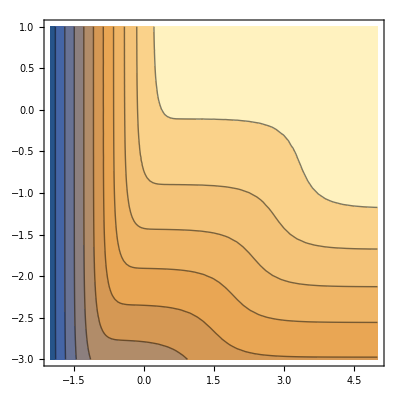

```mathematica
ContourPlot[Log[10,RamanReflect] //. {Iin ->1 , σH->0.0001 σL , σL->10^-pr  κ,d->1}/. κ->10^pκ,{pκ,-2,5},{pr,-3,1},Contours->10]
```

```mathematica
(* We see from the above that once the optical depth is large for the Hα scattering, then the reflection increases by a factor of 2 and whatever passes through decreases like 1/optical depth *)
```

```mathematica
(* These are for different numbers. Have to check what is the case in real life... *)
```

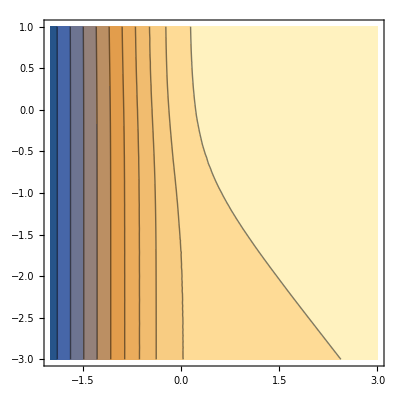

```mathematica
ContourPlot[Log[10,RamanReflect] //. {Iin ->1 , σH->10^pr σL , σL->6 κ,d->1}/. κ->10^pκ,{pκ,-2,3},{pr,-3,1},Contours->10]
```

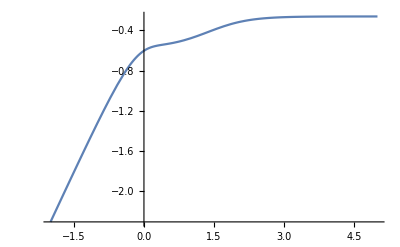

```mathematica
Plot[Log[10,RamanReflect] //. {Iin ->1 , σH-> σL/100 , σL->6 κ,d->1}/. κ->10^pκ,{pκ,-2,5}]
```

```mathematica
(* We have to plug in the opacities and raman absorption as a function of frequency, and plot the results as a function of the column density *)
```